```mathematica
f[x_,n_]:=x^2*Sin[1/x^n]
```

```mathematica
fp1=D[f[x,1],x]
```

-Cos[1/x]+2 x Sin[1/x]

```mathematica
fp2=D[f[x,2],x]
```

-(2 Cos[1/x^2])/x+2 x Sin[1/x^2]

```mathematica
NIntegrate[Sqrt[1+D[f[x,2],x]^2],{x,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.63073×10^-29}. NIntegrate obtained 465.872 and 39.8118 for the integral and error estimates.

465.872

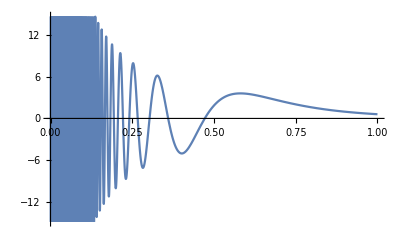

```mathematica
Plot[fp2,{x,0,1}]
```